```mathematica
<<Vilcretas`
```

VilCretas está disponible.

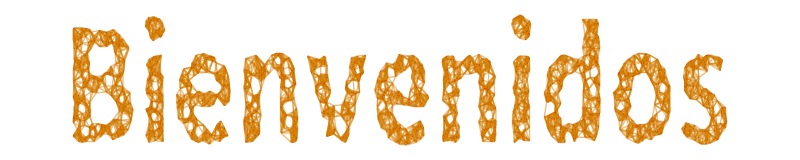

```mathematica
GrafoString["Bienvenidos"]
```

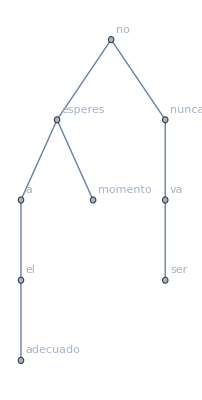

{adecuado,el,a,momento,esperes,ser,va,nunca,no}

4

```mathematica
arbolito =ArbolBinarioBusqueda["no esperes nunca va a ser el momento adecuado"]
?Postfijo
Postfijo[arbolito, "no"]
Altura[arbolito, "no"]
```

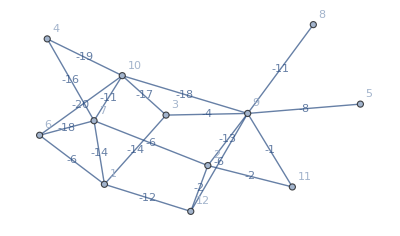

La longitud de un camino más corto es: -98

Iteraciones: (1 | 3 | 6 | 7 | 12 | 2 | 9 | 11 | 10 | 4 | 5 | 8
{∞,{}} | {∞,{}} | {0,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}}
{-6,{6}} | {∞,{}} | {0,{}} | {-18,{6}} | {∞,{}} | {∞,{}} | {∞,{}} | {∞,{}} | {-20,{6}} | {∞,{}} | {∞,{}} | {∞,{}}
{-6,{6}} | {-37,{10}} | {0,{}} | {-31,{10}} | {∞,{}} | {∞,{}} | {-38,{10}} | {∞,{}} | {-20,{6}} | {-39,{10}} | {∞,{}} | {∞,{}}
{-6,{6}} | {-37,{10}} | {0,{}} | {-55,{4}} | {∞,{}} | {∞,{}} | {-38,{10}} | {∞,{}} | {-20,{6}} | {-39,{10}} | {∞,{}} | {∞,{}}
{-69,{7}} | {-37,{10}} | {0,{}} | {-55,{4}} | {∞,{}} | {-61,{7}} | {-38,{10}} | {∞,{}} | {-20,{6}} | {-39,{10}} | {∞,{}} | {∞,{}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-81,{1}} | {-61,{7}} | {-38,{10}} | {∞,{}} | {-20,{6}} | {-39,{10}} | {∞,{}} | {∞,{}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-81,{1}} | {-61,{7}} | {-87,{3}} | {∞,{}} | {-20,{6}} | {-39,{10}} | {∞,{}} | {∞,{}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-93,{9}} | {-100,{9}} | {-87,{3}} | {-88,{9}} | {-20,{6}} | {-39,{10}} | {-95,{9}} | {-98,{9}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-102,{2}} | {-100,{9}} | {-87,{3}} | {-102,{2}} | {-20,{6}} | {-39,{10}} | {-95,{9}} | {-98,{9}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-102,{2}} | {-100,{9}} | {-87,{3}} | {-102,{2}} | {-20,{6}} | {-39,{10}} | {-95,{9}} | {-98,{9}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-102,{2}} | {-100,{9}} | {-87,{3}} | {-102,{2}} | {-20,{6}} | {-39,{10}} | {-95,{9}} | {-98,{9}}
{-69,{7}} | {-83,{1}} | {0,{}} | {-55,{4}} | {-102,{2}} | {-100,{9}} | {-87,{3}} | {-102,{2}} | {-20,{6}} | {-39,{10}} | {-95,{9}} | {-98,{9}})

```mathematica
grafo=Grafo[{{1,3},{1,6},{1,7},{1,12},{2,7},{2,9},{2,11},{2,12},{3,9},{3,10},{4,7},{4,10},{5,9},{6,7},{6,10},{7,10},{8,9},{9,10},{9,11},{9,12}},pesos->-1 {14,6,14,12,6,13,2,2,4,17,16,19,8,18,20,11,11,18,1,6},mostrarpesos->True]

AlDijkstra[grafo,6,8]
```

```mathematica
-Graphics--Graphics-
```

```mathematica
aristas={{a,b},{a,c},{a,e},{b,c},{b,d},{b,e},{c,d},{c,e},{d,d},{c,c},{d,e}};
pes={7,5,2,8,3,14,6,2,6,4,2};
```

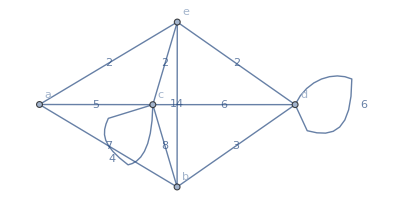

(0 | 7 | 5 | 0 | 2
7 | 0 | 8 | 3 | 14
5 | 8 | 4 | 6 | 2
0 | 3 | 6 | 6 | 2
2 | 14 | 2 | 2 | 0)

```mathematica
graf =Grafo[aristas, pesos->pes, mostrarpesos->True]
MPGrafo[graf, {a,b,c,d,e}]
```

```mathematica
arist ={{1,2},{1,4},{1,5},{1,7},{1,8},{1,10},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{3,5},{3,7},{3,10},{4,5},{4,8},{4,10},{5,6},{5,8},{5,10},{6,8},{6,10},{7,9},{8,9},{8,10},{9,10}};
```

```mathematica
gra=Grafo[arist, dirigido->True]
```

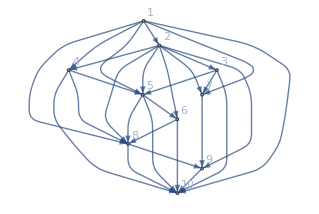
```mathematica
-Graphics-_□
```

```mathematica
Valencias[gra]
```

| 1 | 2 | 4 | 5 | 7 | 8 | 10 | 3 | 6 | 9
Grado o valencia interna | 0 | 1 | 2 | 4 | 3 | 5 | 7 | 1 | 2 | 3
Grado o valencia externa | 6 | 7 | 3 | 3 | 1 | 2 | 0 | 3 | 2 | 1

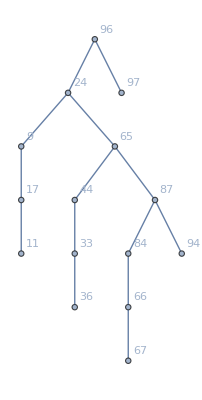

```mathematica
arbol =ArbolBinarioBusqueda[{96,24,65,97,87,84,66,94,44,33,9,36,17,67,11}]
```

```mathematica
Postfijo[arbol, 96]
```

{11,17,9,36,33,44,67,66,84,94,87,65,24,97,96}

```mathematica
Interfijo[arbol, 96]
```

{9,11,17,24,33,36,44,65,66,67,84,87,94,96,97}

```mathematica
KnmCircuitoHamiltonQ[500,500]
```

True

```mathematica
?KnmCircuitoHamiltonQ
```

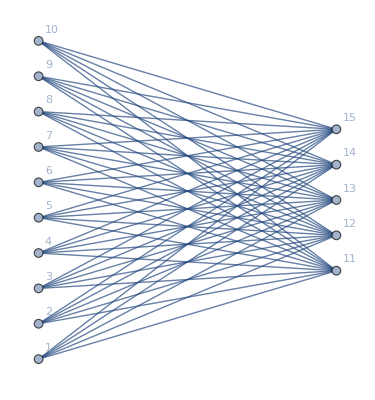

```mathematica
arbolq=GrafoBipartitoCompleto[10,5]
```

```mathematica
ArbolJQ[arbolq]
```

False

Tiene circuitos

```mathematica
grafo3=Grafo[{{a,b},{a,c},{b,c},{b,d},{c,d},{c,e},{c,h},{d,e},{d,f},{e,f},{e,h},{f,g},{f,h},{g,h}},pesos->{3,2,4,2,3,2,6,5,6,4,5,5,5,4},mostrarpesos->True];
```

```mathematica
CircuitoEulerQ[grafo3]
```

False

```mathematica
RutaEulerQ[grafo3]
```

True

```mathematica
CircuitoHamiltonQ[grafo3]
```

True

```mathematica
RutaHamiltonQ[grafo3]
```

True

```mathematica
RutaEuler[grafo3]
```

{{b,a},{a,c},{c,d},{d,e},{e,c},{c,h},{h,e},{e,f},{f,g},{g,h},{h,f},{f,d},{d,b},{b,c}}

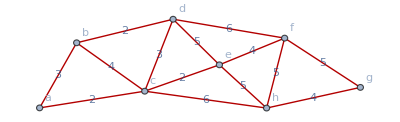

```mathematica
ResaltarRuta[grafo3, {{b,a},{a,c},{c,d},{d,e},{e,c},{c,h},{h,e},{e,f},{f,g},{g,h},{h,f},{f,d},{d,b},{b,c}}]
```

```mathematica
AnimarGrafo[grafo3, {{b,a},{a,c},{c,d},{d,e},{e,c},{c,h},{h,e},{e,f},{f,g},{g,h},{h,f},{f,d},{d,b},{b,c}}]
```

```mathematica
?Prim
```

```mathematica
?Kruskal
```

```mathematica
Prim[grafo3]
```

El orden de los nodos es: {a,b,c,d,e,f,g,h}

T={{a,c},{c,e},{a,b},{b,d},{e,f},{e,h},{h,g}}

Peso: 22

```mathematica
Kruskal[grafo3]
```

T={b<->d,a<->c,c<->e,a<->b,g<->h,e<->f,e<->h}

Peso: 22